### mϕ >> mμ limit

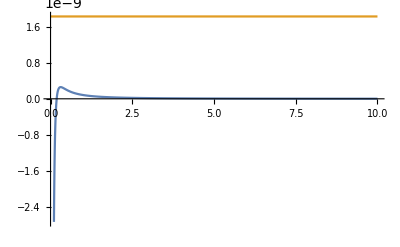

```mathematica
Plot[{(5 10^-11)/mϕ^2(-7/12-Log[0.105/mϕ]),(261-78)10^-11},{mϕ,0,10}]
```

### general fourmula

```mathematica
mμ=0.105;
v=246;
```

```mathematica
Pplus[x_]:=x^2(2-x);
Pminus[x_]:=x^2(-x);
```

```mathematica
Δaμ[mϕ_,α_]:=1/(8 π^2)(mμ/mϕ)^2 NIntegrate[((mμ/v Sin[α])^2 Pplus[x])/((1-x)(1-x (mμ/mϕ)^2)+x(mμ/mϕ)^2),{x,0,1}]
```

```mathematica
Δaμ[0.2,π/2]
```

6.60302×10^-10

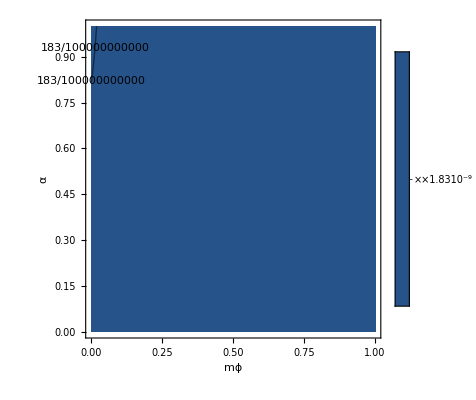

```mathematica
ContourPlot[Δaμ[mϕ,α],{mϕ,0,1},{α,10^-4,1},Contours->{(261-78)10^-11,(287+80)10^-11},PlotLegends->Automatic,PlotRange-> Full,ContourLabels->All, FrameLabel->{"mϕ","α"}]
```

```mathematica
Manipulate[Plot[{Δaμ[mϕ,α],(261-78)10^-11},{mϕ,0,1}],{α,10^-4,2}]
```